```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["output"]
```

C:\Users\Ronak\Dropbox\BridgeToIsland\paper\code\output

Remember to search and replace E -> *10^, e -> *10^ in data files before running below block

```mathematica
angles=Table[1,{i,4}];
angles⟦1⟧=ReadList["angles-1em5.txt"];
angles⟦2⟧=ReadList["angles-1em4.txt"];
angles⟦3⟧=ReadList["angles-1em3.txt"];
angles⟦4⟧=ReadList["angles-1em2.txt"];
sps=ReadList["sprime.txt"];(*This is 𝔰'(ζ)*)
schwTerm=ReadList["energy-terms.txt"];
```

```mathematica
pos=Table[-π/2+(π i)/2000,{i,0,2000-1}];
```

```mathematica
πn=1.0*π
```

3.14159

```mathematica
δζ=(1/2 Max[sps//Re])^-1
```

0.462281

```mathematica
ListPlot[{{pos,angles⟦4⟧}ᵀ,{pos,angles⟦3⟧}ᵀ,{pos,angles⟦2⟧}ᵀ,{pos,angles⟦1⟧}ᵀ,{pos,Sign[#](π-δζ(1-Abs[Sin[#]])/Cos[#])&/@pos}ᵀ},AxesOrigin->{-πn/2,-πn},AxesLabel-> (Style[#,FontSize->16]&/@{"𝔰","ζ"}),PlotLegends->{"2δ=10^-5","2δ=10^-4","2δ=10^-3","2δ=10^-2","ζ=π-1/2.16 (1 - sin 𝔰)/(cos 𝔰)"},PlotTheme->"Classic"]//Rasterize
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

-Graphics-

```mathematica
(*Zooming into the top right of the above plot.*)
ListPlot[#⟦1500;;2000⟧&/@{{pos,angles⟦1⟧}ᵀ,{pos,Sign[#](π-δζ(1-Abs[Sin[#]])/Cos[#])&/@pos}ᵀ},AxesLabel-> (Style[#,FontSize->16]&/@{"𝔰","ζ"}),PlotLegends->{"2δ=10^-5","ζ=π-1/2.16 (1 - sin 𝔰)/(cos 𝔰)"},PlotTheme->"Classic"]//Rasterize
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

-Graphics-

-Graphics-

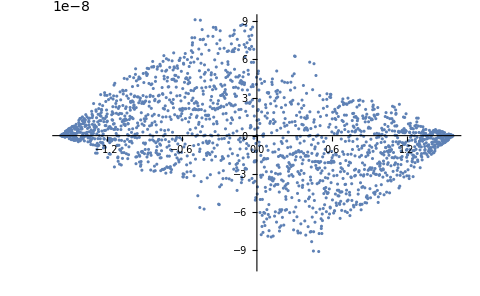

```mathematica
(*Comparing estimated and actual 𝔰'(ζ)*)
ListPlot[{{({pos,sps}ᵀ)⟦1001;;2000⟧,({π+#&/@pos,sps}ᵀ)⟦1;;1000⟧}//Flatten[#,1]&,{({pos,δζ^-1(1+Sin[#])&/@pos}ᵀ)⟦1001;;2000⟧,({π+#&/@pos,δζ^-1(1+Sin[π+#])&/@pos}ᵀ)⟦1;;1000⟧}//Flatten[#,1]&},Axes->True,AxesLabel-> (Style[#,FontSize->16]&/@{"𝔰","𝔰'"}),PlotLegends->{"δ=10^-5","ζ=π-1/2.16 (1 - sin 𝔰)/(cos 𝔰)"},PlotTheme->"Classic"]//Rasterize
ListPlot[{pos,Im[#]&/@sps}ᵀ]
```

```mathematica
(*The actual energy*)
energies=(((4.5 π^2)/Log[.483]^2+1/2-#⟦1⟧)1/(#⟦2⟧)^2-2)&/@({schwTerm,sps}ᵀ);
```

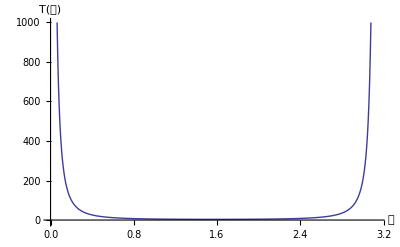

```mathematica
ListPlot[{{pos⟦1001;;2000⟧,energies⟦1001;;2000⟧//Re}ᵀ,{π+pos⟦1;;1000⟧,energies⟦1;;1000⟧//Re}ᵀ}//Flatten[#,1]&,Joined->True,AxesLabel->(Style[#,FontSize->16]&/@{"𝔰","T(𝔰)"}),PlotTheme->"Classic",PlotRange->{{0,π},{-10,1000}},Joined->True]
```

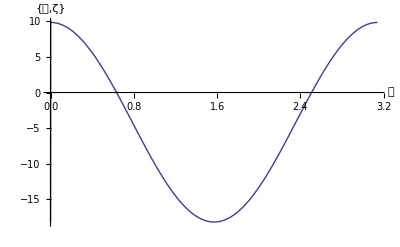

```mathematica
ListPlot[{{pos⟦1001;;2000⟧,schwTerm⟦1001;;2000⟧//Re}ᵀ,{π+pos⟦1;;1000⟧,schwTerm⟦1;;1000⟧//Re}ᵀ}//Flatten[#,1]&,Joined->True,AxesLabel->(Style[#,Bold,FontSize->16]&/@{"𝔰","{𝔰,ζ}"}),PlotTheme->"Classic"(*,PlotRange->{{0,π},{-10,1000}}*),Joined->True]
```